# Lablet locomotion with chemical field sensing

Abhishek Sharma, John McCaskill
BioMIP
Ruhr Universität, Bochum,
Germany

In this calculation, I assume the following variables for simulation : 

Lablet translational velocity : 70 µm/s
Lablet angular velocity : 0.6/s

All the dimensions that will be plotted are in micrometers.

## Using steady state solution to diffusion equation (azimuthal symmetry, cylindrical)

Consider an infinite hollow cylinder with inner and outer radii given by a and b. At steady state, the heat equation in cylindrical coordinates with azimuthal symmetry given by,
             
                                                         ∂/(∂r)(r∂/(∂r)C)=0
                                                         
So, the general solution is given by,

                                                          C(r)=A ln r +B 
                                                         
a = 1 µm
b = 3000 √2 µm
                                                         
Max. concentration : 1 (at a)

Min. concentration :  0.01  (at b)

```mathematica
soln=DSolve[D[r D[c[r],r],r]== 0,c[r],r]//First
```

{c[r]→C[2]+C[1] Log[r]}

```mathematica
soln1=Solve[{(Evaluate[c[r]/.soln]/.r-> a)== Cp,(Evaluate[c[r]/.soln]/.r-> b)== Cb},{C[1],C[2]}]//First
```

{C[1]→-(Cb-Cp)/(Log[a]-Log[b]),C[2]→-(-Cb Log[a]+Cp Log[b])/(Log[a]-Log[b])}

```mathematica
ConcCyl[{x_,y_},{Cp_,Cb_},{a_,b_}]=Evaluate[c[r]/.soln/.soln1/.r->√(x^2+y^2)//FullSimplify]
```

(Cb Log[a]-Cp Log[b]+1/2 (-Cb+Cp) Log[x^2+y^2])/(Log[a]-Log[b])

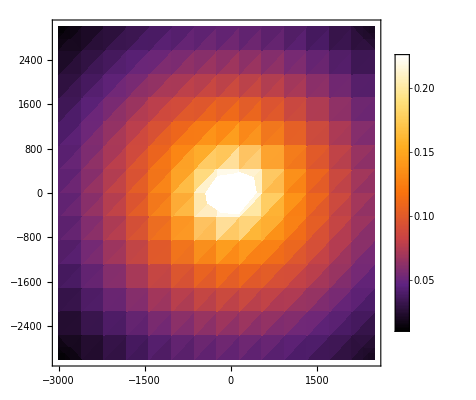

```mathematica
DensityPlot[ConcCyl[{x,y},{1,0.01},{0.1,3000 √2}],{x,-3000,2500},{y,-3000,3000},ColorFunction->"SunsetColors",PlotLegends-> Automatic]
```

## Using steady state solution to diffusion equation (azimuthal and poloidal symmetry, spherical)

Considering a hollow sphere with inner and outer radii given by a and b. At steady state, the heat equation in spherical coordinates with azimuthal and poloidal symmetry becomes, 
                                      

                                                   ∂/(∂r)(r^2∂/(∂r))=0

```mathematica
soln=DSolve[D[r^2 D[c[r],r],r]== 0,c[r],r]//First
```

{c[r]→-C[1]/r+C[2]}

```mathematica
soln1=Solve[{(Evaluate[c[r]/.soln]/.r-> a)== Cp,(Evaluate[c[r]/.soln]/.r-> b)== Cb},{C[1],C[2]}]//First
```

{C[1]→-(a b (Cb-Cp))/(a-b),C[2]→-(b Cb-a Cp)/(a-b)}

```mathematica
ConcSph[{x_,y_},{Cp_,Cb_},{a_,b_}]=Evaluate[c[r]/.soln/.soln1/.r->√(x^2+y^2)]//FullSimplify
```

(-b Cb+a Cp+(a b (Cb-Cp))/(√(x^2+y^2)))/(a-b)

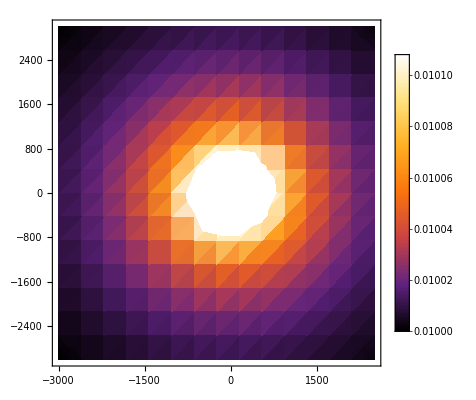

```mathematica
DensityPlot[ConcSph[{x,y},{1,0.01},{0.1,3000 √2}],{x,-3000,2500},{y,-3000,3000},ColorFunction->"SunsetColors",PlotLegends-> Automatic,PlotRange->Automatic,MaxRecursion->10,WorkingPrecision->10]
```

## Chemical walk for Lablets for cylindrical coordinates

### Numerical formulation together with random noise in displacement and noise in sensor opeartions

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0.;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0.;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.1;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=2000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
(*If[Y1≤ 0,Y1=0];*)
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={-2000,2000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1};(* Operation for Case : C1 > C2 *)
seqX2={1,1,1};(* Operation for Case : C1 < C2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

C1=ConcCyl[{X,Y},{1,0.01},{0.1,3000 √2}]+ΔcR RandomReal[NormalDistribution[0,1]];
(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

C2=ConcCyl[{X,Y},{1,0.01},{0.1,3000 √2}]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,If[C2-C1>0,updateSeq=seqX1,updateSeq=seqX2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{{C1,C2}}]],op];
dataConc];
```

#### Adding noise to concentration

```mathematica
dataConc1=simFunc[θR,ΔxR,ΔyR,0.005,2,vLablet,ωLablet];
```

```mathematica
dataConc2=simFunc[θR,ΔxR,ΔyR,0.01,2,vLablet,ωLablet];
```

```mathematica
dataConc3=simFunc[θR,ΔxR,ΔyR,0.02,2,vLablet,ωLablet];
```

```mathematica
dataConc4=simFunc[θR,ΔxR,ΔyR,0.05,2,vLablet,ωLablet];
```

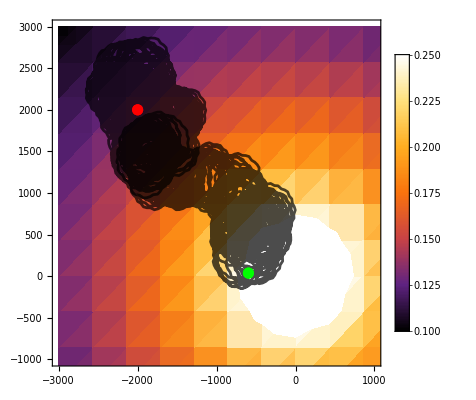

```mathematica
Show[{DensityPlot[ConcCyl[{i,j},{1,0.1},{0.1,3000 √2}],{i,-3000,3000},{j,-3000,3000},ColorFunction->"SunsetColors",PlotRange->{{-3000,1000},{-1000,3000},{0.1,0.25}},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize-> 120],Right],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]}],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,AspectRatio-> 1,PlotStyle->Directive[Opacity[0.7],Black]],ListPlot[{dataPos⟦All,1;;2⟧//First},PlotStyle->{ PointSize[0.02],Red}],ListPlot[{dataPos⟦All,1;;2⟧//Last},PlotStyle->{ PointSize[0.02],Green}]},AspectRatio->1]
```

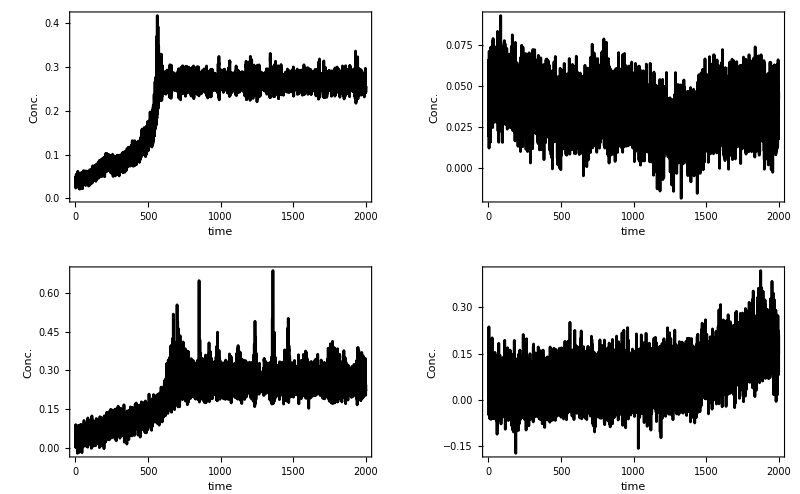

```mathematica
GraphicsGrid[Partition[{ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc4]]],Flatten[dataConc4]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full]},2],Frame-> All]
```

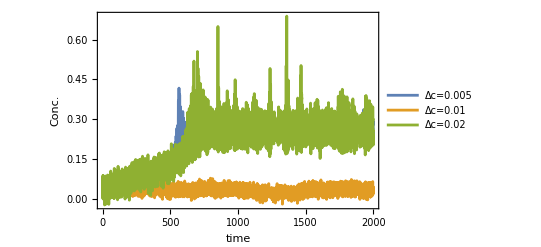

```mathematica
ListPlot[{MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}]},Joined-> True,PlotStyle->Automatic,Frame-> True,FrameLabel-> {"time","Conc."},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full,PlotLegends->Placed[ {"Δc=0.005","Δc=0.01","Δc=0.02","Δc=0.05"},{0.125,0.8}]]
```

#### Adding random displacement

```mathematica
dataConc1=simFunc[θR,1,1,0.01,2,vLablet,ωLablet];
```

```mathematica
dataConc2=simFunc[θR,5,5,0.01,2,vLablet,ωLablet];
```

```mathematica
dataConc3=simFunc[θR,10,10,0.01,2,vLablet,ωLablet];
```

```mathematica
dataConc4=simFunc[θR,20,20,0.01,2,vLablet,ωLablet];
```

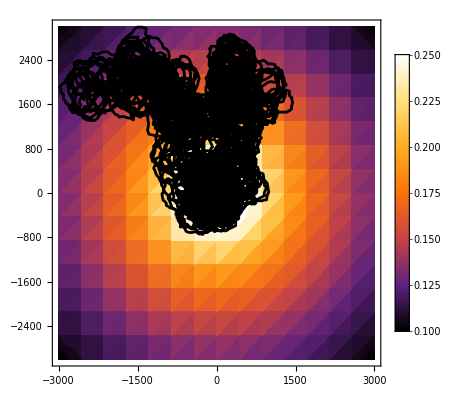

```mathematica
Show[{DensityPlot[ConcCyl[{i,j},{1,0.1},{0.1,3000 √2}],{i,-3000,3000},{j,-3000,3000},ColorFunction->"SunsetColors",PlotRange->{{-3000,3000},{-3000,3000},{0.1,0.25}},PlotLegends->Automatic],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,AspectRatio-> 1,PlotStyle->Black]},AspectRatio->1]
```

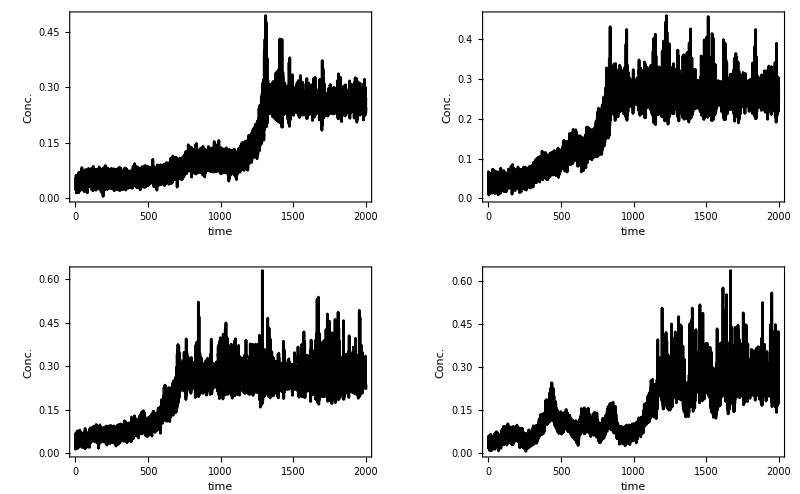

```mathematica
GraphicsGrid[Partition[{ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc4]]],Flatten[dataConc4]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full]},2],Frame-> All]
```

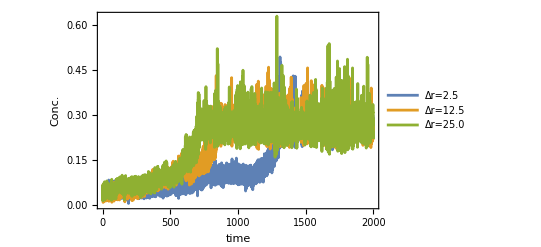

```mathematica
ListPlot[{MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}]},Joined-> True,PlotStyle->Automatic,Frame-> True,FrameLabel-> {"time","Conc."},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full,PlotLegends-> Placed[{"Δr=2.5","Δr=12.5","Δr=25.0"},{0.1,0.8}]]
```

## Chemical walk for Lablets for two electrode geometry

```mathematica
ClearAll["Global`*"]
```

### Creating concentration field from one dimensional

```mathematica
e=UnitConvert[Quantity["ElectronCharge"]];
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]];
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]];
```

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]];
```

```mathematica
T=UnitConvert[Quantity[298.,"Kelvin"]];
```

```mathematica
ApplV=Quantity[0.5,"V"]; (* Applied Voltage *)
```

```mathematica
DiffC=Quantity[1 10^-9,"m^2/s"]; (* Diffusion constant *)
```

```mathematica
chL=Quantity[1 10^-2,"m"];(* Length scale for simulation *)
```

```mathematica
bulkC=Quantity[10. ,"mol/m^3"];
```

```mathematica
z=1;(* Valence *)
```

```mathematica
JLim=(2 z e DiffC bulkC NA)/chL
```

0.192971 A/m^2

```mathematica
VTh=(kB T)/e//UnitSimplify;(* Thermal Voltage *)
```

```mathematica
V =ApplV/VTh;(* Dimensionless Voltage *)
```

```mathematica
J = Tanh[V/4.];
```

```mathematica
Conc[ω_]:= 1 +J Re[ω];
```

```mathematica
K=0.1;
```

```mathematica
Pot[ω_] := Log[(1 + J Re[ω])/(K(1-J^2))];
```

#### Conformal map to coplanar geometry from parallel plate geometry

```mathematica
Clear[t,t1,t2,t3,t4]
```

```mathematica
(* Changing from the T Space to U Space *)
f0[t_]=∫C/(√((t-t1)(t-t2)(t-t3)(t-t4)))ⅆt;
```

```mathematica
FullSimplify[f0[t]]
(* Simplifying this gives the following Form,  the constant C is calculated from the complete Integral, F(t3) = 1 *)
```

(2 C √(t-t1) √(t-t2) √(((t1-t2) (t-t3))/((t-t2) (t1-t3))) (t-t4) EllipticF[ArcSin[(√(t-t1) √(t2-t4))/(√(t-t2) √(t1-t4))],((t2-t3) (t1-t4))/((t1-t3) (t2-t4))])/(√((t-t1) (t-t2) (t-t3) (t-t4)) √(((t1-t2) (t-t4))/((t-t2) (t1-t4))) √(t1-t4) √(t2-t4))

```mathematica
f[t_]= (2C)/(√((t2-t3)(t1-t4))) EllipticF[ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))];
f1[t_] =  EllipticF[ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))];
```

```mathematica
aa=Chop[EllipticF[ArcSin[√(((t3-t2) (t1-t4))/((t3-t1) (t2-t4)))],((t1-t3) (t2-t4))/((t2-t3) (t1-t4))]];
```

```mathematica
g[t_] := ArcSin[√(((t-t2) (t1-t4))/((t-t1) (t2-t4)))];
 p = ((t1-t3) (t2-t4))/((t2-t3) (t1-t4));
(* Complete Elliptical Integral*)
iK = EllipticK[p];
t1=-1.5;t2=-0.5;t3=0.5;t4=1.5; (* Assumed *)
FF[t_] = f1[t]/aa;
```

```mathematica
p1=ParametricPlot[With[{ω=u+I v},{Re[ω],Im[ω]}],{u,0,1},{v,0,1}, Mesh-> Full,MeshStyle-> {Red}];
```

```mathematica
p2=ParametricPlot[With[{ω=u+I v,b= FF[u+I v] },{Re[b],Im[b]}],{u,-1,1},{v,0,1}, Mesh-> Full,MeshStyle-> {Red},PlotRange-> {0.,0.9}];
```

```mathematica
(* Trying to make the Invert Plots for the same *)
```

```mathematica
FK[u_,v_] = Flatten[Solve[f1[t]== aa (u+I v),t]]⟦1,2⟧;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
p3=ParametricPlot[With[{ω=u+I v,b= FK[u,v] },{Re[b],Im[b]}],{u,0,2},{v,0,0.78},MeshStyle->{Red},Mesh-> {20,20},AspectRatio->0.6];
```

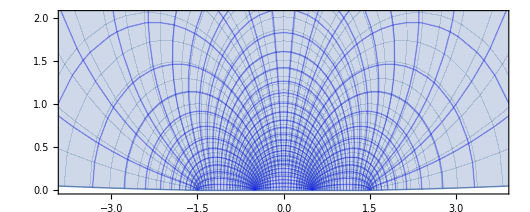

```mathematica
ParametricPlot[With[{ω=u+I v,b= FK[u,v]},{Re[b],Im[b]}],{u,0,1},{v,0,0.78},Mesh-> {30,30},MeshStyle-> Blue]
```

#### Solution for coplanar geometry

```mathematica
p1=ListContourPlot[Flatten[Table[{Re[FK[u,v]],Im[FK[u,v]],Conc[u + I v] },{u,0,1,0.01},{v,0,0.78,0.01}],1],Contours->20,ContourLabels-> None,ColorFunction->"DarkRainbow",PlotRange->{{-5,5},{0,5},All}];
```

```mathematica
p2=ListContourPlot[Flatten[Table[{Re[FK[u,v]],Im[FK[u,v]],Pot[u + I v] },{u,0,1,0.01},{v,0,0.78,0.01}],1],Contours->20,ContourLabels-> None,ColorFunction->"DarkRainbow",PlotRange->{{-5,5},{0,5},All}];
```

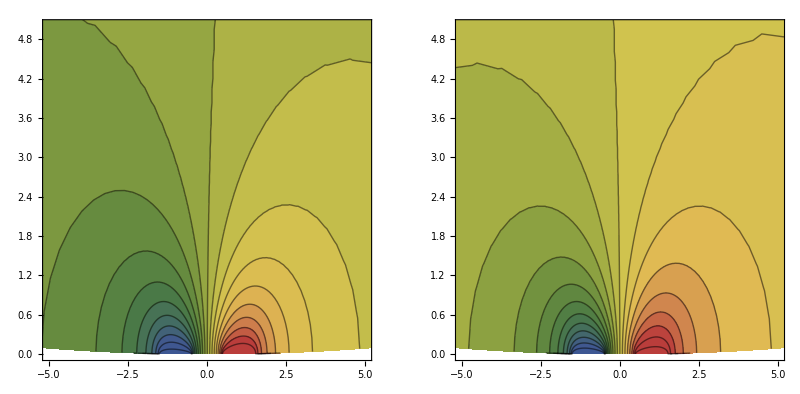

```mathematica
GraphicsRow[{p1,p2},Frame-> All]
```

```mathematica
scale=2000.;
```

```mathematica
intp1=Interpolation[Flatten[Table[{scale{Re[FK[u,v]],Im[FK[u,v]]},Conc[u+I v]},{u,0,1,0.005},{v,0,0.79,0.005}],1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-166253., 166254.}, {-281114., 545229.}}, <>]

```mathematica
intp2=Interpolation[Flatten[Table[{scale{Re[FK[u,v]],Im[FK[u,v]]},Pot[u+I v]},{u,0,1,0.005},{v,0,0.79,0.005}],1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-166253., 166254.}, {-281114., 545229.}}, <>]

```mathematica
GraphicsRow[{DensityPlot[intp1[i,j],{i,-10000,10000},{j,0,10000},PlotRange->{{-10000,10000},{0,10000},All},ColorFunction->"SunsetColors",PlotLegends->Automatic],DensityPlot[intp2[i,j],{i,-10000,10000},{j,0,10000},PlotRange->{{-10000,10000},{0,10000},All},ColorFunction->"SunsetColors",PlotLegends->Automatic]},Frame-> All]
```

-Graphics-

### Numerical formulation together with random noise in displacement and noise in sensor operations

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.01;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=3000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
If[Y1≤ 0,Y1=0];
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
If[Y1≤ 0,Y1=0];
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={-3000,3000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0,0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1};(* Operation for Case : C1 > C2 *)
seqX2={1,1,1};(* Operation for Case : C1 < C2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

C1=intp1[X,Y]+ΔcR RandomReal[NormalDistribution[0,1]];
(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

C2=intp1[X,Y]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,If[C2-C1>0,updateSeq=seqX1,updateSeq=seqX2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{{C1,C2}}]],op];
dataConc];
```

```mathematica
dataConc1=simFunc[θR,ΔxR,ΔyR,0.005,2,vLablet,ωLablet];
```

```mathematica
dataPosX1=dataPos;
```

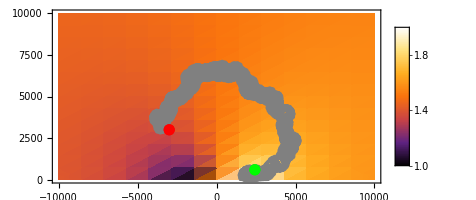

```mathematica
p1=Show[{DensityPlot[intp1[i,j],{i,-10000,10000},{j,0,10000},ColorFunction->"SunsetColors",LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange->{{-10000,10000},{0,10000},All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize-> 120],Right]],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,PlotRange-> All,AspectRatio-> 0.5,PlotStyle->Gray],ListPlot[{dataPos⟦All,1;;2⟧//First},PlotStyle->{ PointSize[0.02],Red}],ListPlot[{dataPos⟦All,1;;2⟧//Last},PlotStyle->{ PointSize[0.02],Green}]},AspectRatio->0.5]
```

```mathematica
dataConc2=simFunc[θR,ΔxR,ΔyR,0.01,2,vLablet,ωLablet];
```

```mathematica
dataConc3=simFunc[θR,ΔxR,ΔyR,0.02,2,vLablet,ωLablet];
```

```mathematica
dataConc4=simFunc[θR,ΔxR,ΔyR,0.05,2,vLablet,ωLablet];
```

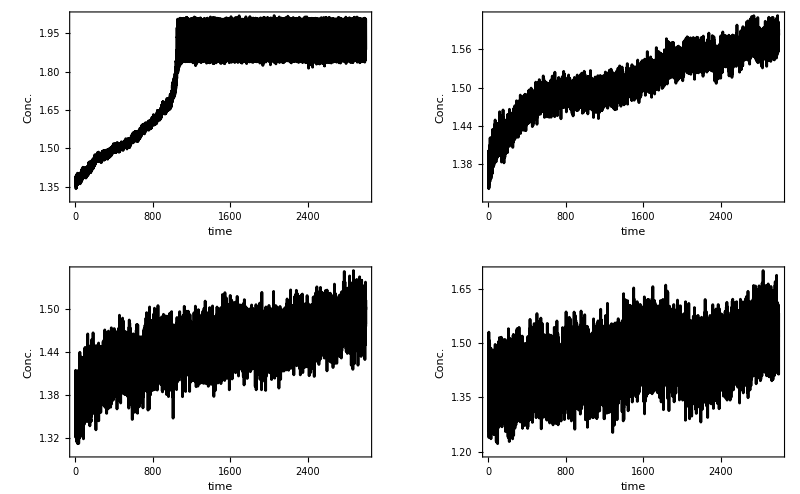

```mathematica
GraphicsGrid[Partition[{ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full],ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc4]]],Flatten[dataConc4]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Conc."},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full]},2],Frame-> All]
```

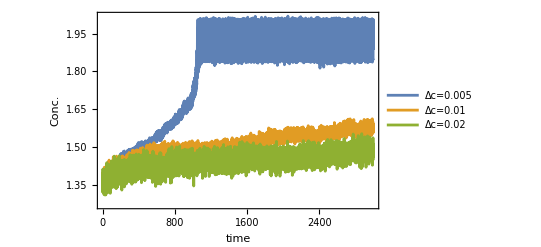

```mathematica
ListPlot[{MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc1]]],Flatten[dataConc1]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc2]]],Flatten[dataConc2]}],MapThread[{(dt/2.)#1,#2}&,{Range[Length[Flatten[dataConc3]]],Flatten[dataConc3]}]},Joined-> True,PlotStyle->Automatic,Frame-> True,FrameLabel-> {"time","Conc."},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full,PlotLegends->Placed[ {"Δc=0.005","Δc=0.01","Δc=0.02","Δc=0.05"},{0.125,0.8}]]
```

#### Tracking orientation of Lablet and starting from different places....

```mathematica
θR=0;(* maximum random change in angle per time step *)
```

```mathematica
ΔxR=0;(* maximum random displacement along X per time step *)
```

```mathematica
ΔyR=0;(* maximum random displacement along Y per time step *)
```

```mathematica
ΔcR=0.01;(* maximun noise noise in sensor measurement *)
```

```mathematica
Δt=0.4;(* Switching times for Lablet, also time step *)
```

```mathematica
dt=0.4;(* time step for simulation *)
```

```mathematica
tT=1000;(* Total time of simulation *)
```

```mathematica
tSteps=tT/dt;
```

```mathematica
vLablet=70.;ωLablet=0.6;α=π/12;
```

```mathematica
ntS=2; (* Number of steps after with switching operation takes place *)
```

```mathematica
nOp=(tT/Δt);
```

```mathematica
simFunc[θR_,ΔxR_,ΔyR_,ΔcR_,ntS_,v_,ω_]:=Module[{mType1,mType2},
mType1[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+θR RandomReal[NormalDistribution[0,1]];
X1=X+2v Cos[Θ1]dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+2v Sin[Θ1]dt+ΔyR RandomReal[NormalDistribution[0,1]];
If[Y1≤ 0,Y1=0];
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
mType2[{X_,Y_,Θ_}]:=Module[{X1,Y1,Θ1},Θ1=Θ+ω dt+θR RandomReal[NormalDistribution[0,1]];
X1=X+v( Cos[Θ](1+Sin[α])-Cos[α]Sin[Θ])dt+ΔxR RandomReal[NormalDistribution[0,1]];
Y1=Y+v( Cos[α]Cos[Θ]+(1+Sin[α])Sin[Θ])dt+ΔyR RandomReal[NormalDistribution[0,1]];
If[Y1≤ 0,Y1=0];
dataPos=Join[dataPos,{{X1,Y1,Θ1}}];
{X1,Y1,Θ1}];
(* Running simulation *)
iPos={5000,5000};iθ=π/3;
dataPos={{iPos⟦1⟧,iPos⟦2⟧,iθ}};
dataConc={};

Monitor[For[op=1,op≤nOp,op++,
stSeq1={0,0}; (* Standard translational sequence *)
stSeq2={1,1};(* Standard rotational sequence *)

seqX1={1};(* Operation for Case : C1 > C2 *)
seqX2={1,1,1};(* Operation for Case : C1 < C2 *)

X=Last[dataPos]⟦1⟧ ;Y=Last[dataPos]⟦2⟧;Θ=Last[dataPos]⟦3⟧;(* Initializing position and orientation *)

C1=intp1[X,Y]+ΔcR RandomReal[NormalDistribution[0,1]];
(* Standard translation operation *)
SeqOp=Flatten[ConstantArray[stSeq1⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[stSeq1]]];
ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];

C2=intp1[X,Y]+ΔcR RandomReal[NormalDistribution[0,1]];
If[Mod[op,ntS]== 0,If[C2-C1>0,updateSeq=seqX1,updateSeq=seqX2],updateSeq=stSeq2];
SeqOp=Flatten[ConstantArray[updateSeq⟦#⟧,{IntegerPart[(Δt/dt)]}]&/@Range[Length[updateSeq]]];
ns=1;ns=1;While[ns≤Length[SeqOp],cOp=SeqOp⟦ns⟧;
{X,Y,Θ}=Which[cOp== 0,mType1[{X,Y,Θ}],cOp== 1,mType2[{X,Y,Θ}]];ns++];dataConc=Join[dataConc,{{C1,C2}}]],op];
dataConc];
```

```mathematica
dataConcx=simFunc[θR,ΔxR,ΔyR,0.005,2,vLablet,ωLablet];
```

```mathematica
dataPosX2=dataPos;
```

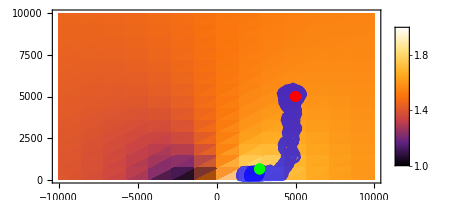

```mathematica
p2=Show[{DensityPlot[intp1[i,j],{i,-10000,10000},{j,0,10000},ColorFunction->"SunsetColors",PlotRange->{{-10000,10000},{0,10000},All},PlotLegends->Automatic],ListPlot[dataPos⟦All,1;;2⟧,Joined-> True,PlotRange-> All,AspectRatio-> 0.5,PlotStyle->Directive[Opacity[0.7],Blue]],ListPlot[{dataPos⟦All,1;;2⟧//First},PlotStyle->{ PointSize[0.02],Red}],ListPlot[{dataPos⟦All,1;;2⟧//Last},PlotStyle->{ PointSize[0.02],Green}]},AspectRatio->0.5]
```

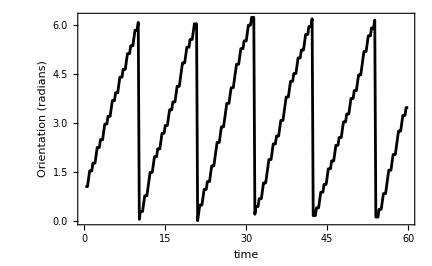

```mathematica
ListPlot[MapThread[{(dt/2.)#1,#2}&,{Range[300],Mod[dataPos⟦1;;300,3⟧,2π]}],Joined-> True,Frame-> True,FrameLabel-> {"time","Orientation (radians)"},PlotStyle-> Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange-> Full]
```

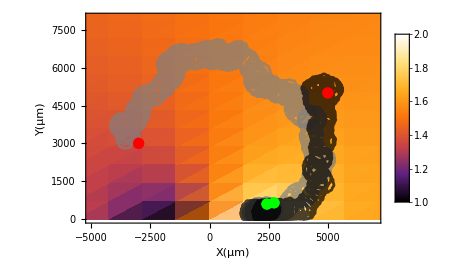

```mathematica
Show[{DensityPlot[intp1[i,j],{i,-10000,10000},{j,0,10000},ColorFunction->"SunsetColors",FrameLabel-> {"X(µm)","Y(µm)"},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize-> 12]},PlotRange->{{-5000,7000},{0,8000},All},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize-> 120],Right]],ListPlot[dataPosX1⟦All,1;;2⟧,Joined-> True,PlotRange-> All,AspectRatio-> 0.5,PlotStyle->Directive[Opacity[0.7],Gray]],
ListPlot[dataPosX2⟦All,1;;2⟧,Joined-> True,PlotRange-> All,AspectRatio-> 0.5,PlotStyle->Directive[Opacity[0.7],Black]],
ListPlot[{dataPosX1⟦All,1;;2⟧//First},PlotStyle->{ PointSize[0.02],Red}],ListPlot[{dataPosX1⟦All,1;;2⟧//Last},PlotStyle->{ PointSize[0.02],Green}],ListPlot[{dataPosX2⟦All,1;;2⟧//First},PlotStyle->{ PointSize[0.02],Red}],ListPlot[{dataPosX2⟦All,1;;2⟧//Last},PlotStyle->{ PointSize[0.02],Green}]},AspectRatio->0.66]
```